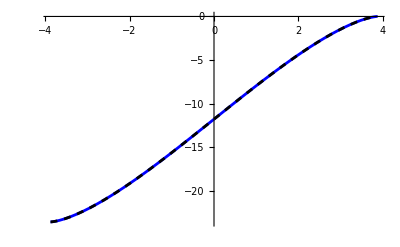

Cos[-(2 z^(3/2))/3+π/4+O[1/z]^(3/2)] ((1/z)^(1/4)/(√π)+O[1/z]^(5/4))+(-(5 (1/z)^(7/4))/(48 √π)+O[1/z]^2) Sin[-(2 z^(3/2))/3+π/4+O[1/z]^(3/2)]

-1599.07

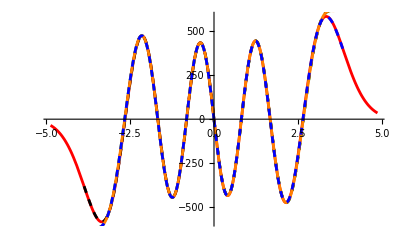

```mathematica
Clear[n]
n:=7;
h:=1;
e:=h*( n+1/2);
S1[x_,n_]:=1/4 (π+2 n π+2 x √(1+2 n-x^2)+(2+4 n) ArcTan[x/(√(1+2 n-x^2))]);
S2[x_,n_]:=-S1[x,n];
S1right[x_,n_]:=S1[x,n]-Pi*h*(n+1/2);
S1rightnew[x_,n_]:=1/2 (-e π+x √(2 e-x^2)+2 e ArcTan[x/(√(2 e-x^2))]);
Plot[{S1right[x,n],S1rightnew[x,n]},{x,x1,x2},PlotStyle->{Blue,{Black,Dashed}}]
J[x_]:=Sqrt[2*e-x^2];
x1:=-Sqrt[2*e];
x2:=Sqrt[2*e];
F[x_]:=1/Sqrt[J[x]]*2*Cos[S1[x,n]/h-Pi/4];
G[x_]:=Exp[-x^2/(2*h)]*HermiteH[n,x/Sqrt[h]];
z[x_]:=CubeRoot[(3/2*Abs[S1[x,n]])^2];
zright[x_]:=CubeRoot[(3/2*Abs[S1rightnew[x,n]])^2];

(*con:=(((Re[Exp[I*S1[x,n]/h]/Sqrt[Abs[J[x]]]+Exp[-I*Pi/2]*Exp[-I*S1[x,n]/h]/Sqrt[Abs[J[x]]]]))/.x->-0.5)/((Exp[-x^2/(2*h)]*HermiteH[n,x/Sqrt[h]])/.x->-0.5);
N[((1/Sqrt[J[x]]*2*Cos[S1[x,n]/h-Pi/4])/.x->-0.5)]
N[(Exp[-x^2/(2*h)]*HermiteH[n,x/Sqrt[h]])/.x->-0.5]
N[406.8310720914985/-0.9550155942603145]*)
Series[AiryAi[-z],{z,Infinity,1}]
N[1/con]
Show[(*Plot[con*ParabolicCylinderD[5,√2 x],{x,x1,x2},PlotStyle->Red],*)
Plot[Exp[-x^2/(2*h)]*HermiteH[n,x/Sqrt[h]],{x,x1-1,x2+1},PlotStyle->Red],(*Plot[1/con*(Re[Exp[I*S1[x,n]/h]/Sqrt[Abs[J[x]]]+Exp[-I*Pi/2]*Exp[-I*S1[x,n]/h]/Sqrt[Abs[J[x]]]]),{x,x1,x2},PlotStyle->Dashed],*)Plot[(G[0.5]/F[0.5])*1/Sqrt[J[x]]*2*Cos[S1[x,n]/h-Pi/4],{x,x1,x2},PlotStyle->{Green,Dashed}],Plot[(G[0.5]/F[0.5])*1/Sqrt[J[x]]*2*AiryAi[-z[x]]*Sqrt[Pi]*Sqrt[Sqrt[Abs[z[x]]]],{x,x1,x2},PlotStyle->{Black,Dashed}],Plot[(G[0.5]/F[0.5])*1/Sqrt[J[x]]*2*(-1)^n*Cos[Pi/4+S1rightnew[x,n]/h],{x,x1,x2},PlotStyle->{Orange}],Plot[(G[0.5]/F[0.5])*1/Sqrt[J[x]]*2*(-1)^n*AiryAi[-zright[x]]*Sqrt[Pi]*Sqrt[Sqrt[Abs[zright[x]]]],{x,x1,x2},PlotStyle->{Blue,Dashed}]]
```

```mathematica
Limit[1/Sqrt[J[x]]*2*Cos[S1[x,n]/h-Pi/4],x->x1+0.00001]
Limit[S1[x,n],x->x1+0.00001]
Limit[J[x],x->x1]
```

15.6705

5.42965×10^-8

0